the area of S^3= 2 π^2 R^3, or volume of this 3D S^3universe

2 π^2 R^3

2 π^2 R^3

area of S^3, or the 3D volume as a function of ρ, for example from F-W metric etc...

2 π R^3 (ρ-Cos[ρ] Sin[ρ])

the 2D area of the 3D manifold == 'area' of S^3 of radius R

2 π R^3 (1-Cos[ρ]^2+Sin[ρ]^2)

the 2D area of a shell, the surface of a 3D manifold == 'area' of S^3 of radius R

calculate the area of S^3 by analogously integrating over ρ a set of  S^2 shells with increasing radius multiplied by dρ

2 π^2 R^3

area of S^3 of radius R == volume of the 'surface'  of a 4D sphere of radius R

2 π^2 R^3

1

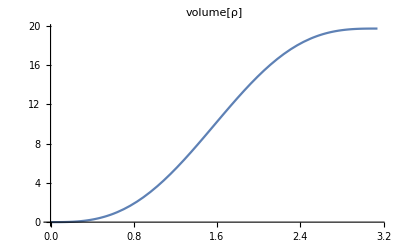

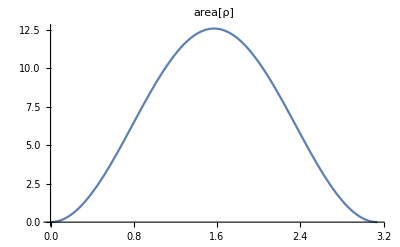

```mathematica
(* S^3 Universe *)
Print["the area of S^3= 2 π^2 R^3, or volume of this 3D S^3universe "]
R^3 Integrate[1/Sqrt[1-p^2] p^2 Sin[ψ],{p,-1,1},{ψ,0,π},{θ,0,2π}]
2 R^3 Integrate[1/Sqrt[1-p^2] p^2 Sin[ψ],{p,0,1},{ψ,0,π},{θ,0,2π}]

(* volume and area in S^3 Universe as a function of ρ = l/R, where l is the manifold distance 
(measured distance) and R is the radius of 4D ball *)
(* area of S^3, the 3D volume as a function of ρ, for example from F-W metric etc...*)
Print["area of S^3, or the 3D volume as a function of ρ, for example from F-W metric etc..."]
vol=2 π R^3(ρ -Sin[ρ]Cos[ρ])
Print["the 2D area of the 3D manifold == 'area' of S^3 of radius R "]
area=D[vol,ρ]

(* now check the area of S^3 by analogously integrating over ρ a set of a set of shells S^2 with increasing radius multiplied by dρ *)
Print["the 2D area of a shell, the surface of a 3D manifold == 'area' of S^3 of radius R"]
Print["calculate the area of S^3 by analogously integrating over ρ a set of  S^2 shells with increasing radius multiplied by dρ"]
Integrate[2 π R^3 (1-Cos[ρ]^2+Sin[ρ]^2), {ρ,0,  π}]
(* area of S^3 of radius R *)
Print["area of S^3 of radius R == volume of the 'surface'  of a 4D sphere of radius R "]
volπ=2 π^2 R^3
(* plot, put RR=1 *)
RR=1
Plot[2 π RR^3(ρ-Sin[ρ]Cos[ρ]), {ρ,0,  π},PlotLabel->"volume[ρ]"]
Plot[2 π RR^3 (1-Cos[ρ]^2+Sin[ρ]^2),{ρ,0,  π},PlotLabel->"area[ρ]"]
```

180/π

57.2958

Nsc is number of supeclusters

10000000

2000000

10

1.95275×10^6

98927.7

radius of 4D sphere in Mps

462.494

V

1.95275×10^9

rho

0.00102419

1452.97

145.297

145

0.0216662

145

1/2 (1+√2)

1

normalization checks: should be Nsc

2.×10^6

normalization checks: should be 1

1.

average separation degrees

2.×10^6

1.

0.963192

average separation degrees weighted by luminosity with simple 1/r^2 dependence

841.136

4.07199

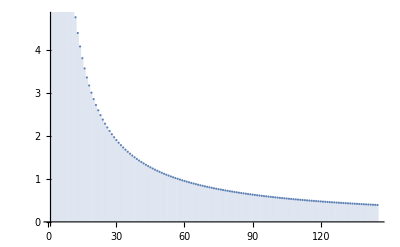

145/4

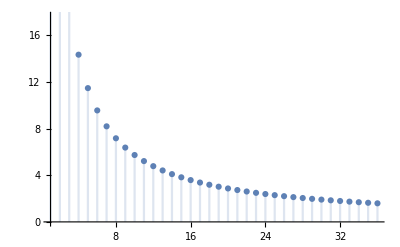

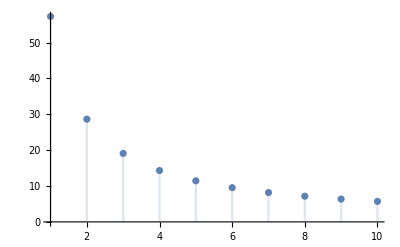

1.79185×10^6

0.895927

3.99346

different, I believe correct, normalization with simple 1/r^2 dependence and with ArcTan

2.×10^6

1.

3.57785

average separation degrees weighted by luminosity in S^3 with the correct 1/area dependence and ArcTan

0.0032176

1.6088×10^-9

2.16076

separation angle after slicing in S^3as a function of ρ

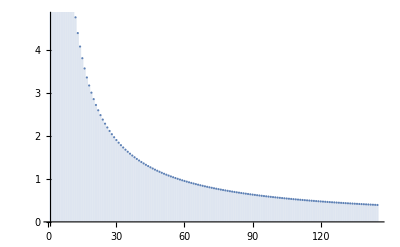

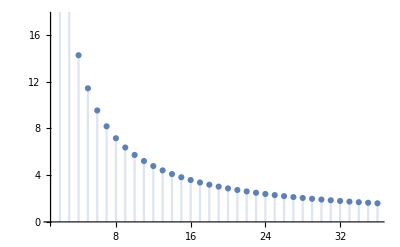

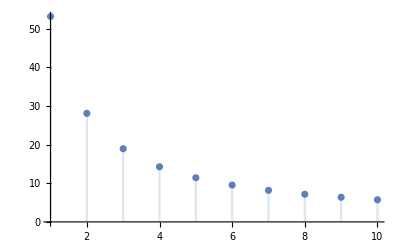

the distribution of the separation angle, after slicing in S^3 and weighted by the slice volume

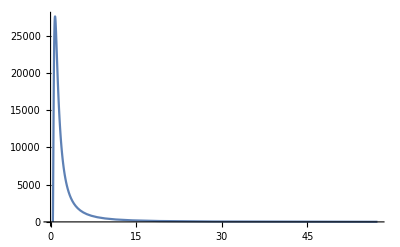

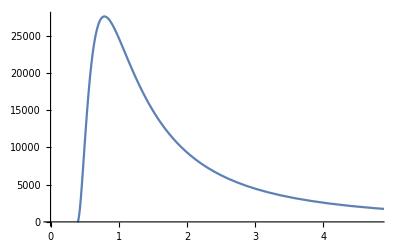

-Graphics-

-Graphics-

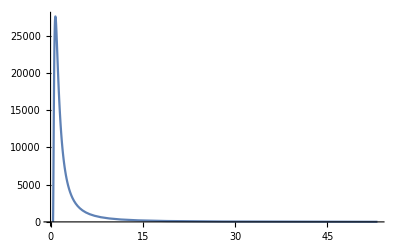

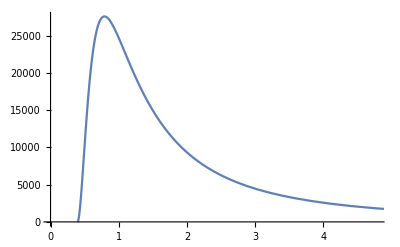

```mathematica
(* calculate numerically the angular separation of supeclusters and voids 
treat superclusters as points at the vertices of 3D cubical voids *)
(* number of superclusters Nsc = 10^7 *)
(* number of voids Nv 
Nsc=(Nv+1)^3 
Nv=Nsc^(1/3) -1 *)
(* volume V=Nv Dv^3 = 2 π^2 R^3
or
R ={Nv/(2 π^2)}^(1/3) Dv = (1/(2 π^2)^(1/3)(Nsc^(1/3)-1) DV
*)
degRad=180/π
%//N
Print["Nsc is number of supeclusters"]
Nsc = 1 10^7
Nsc = 2 10^6
Dv=10
Nv=(Nsc^(1/3)-1)^3//N
Nv/2/π^2
Print["radius of 4D sphere in Mps"]
R=(Nv/(2 π^2))^(1/3) Dv
Print["V"]
V=2 π^2 R^3
Print["rho"]
rho=Nsc/V
L=π R
L/Dv
Nbin=Round[L/Dv]
delta=π/Nbin//N
Lbin=Nbin
corr=(1+Sqrt[2])/2
corr=1
Print["normalization checks: should be Nsc"]
Ncheck=Sum[2 π R^3 (1-Cos[i delta]^2+Sin[i delta]^2)delta rho,{i,Lbin}]
Print["normalization checks: should be 1"]
Ncheck=Sum[2 π R^3 (1-Cos[i delta]^2+Sin[i delta]^2)delta rho,{i,Lbin}]/Nsc
(*
For[i=0,i<Nbin+1,i++,Print[2 π R^3 (1-Cos[i delta]^2+Sin[i delta]^2)delta rho]]
*)
Print["average separation degrees"]
Ncheck= Sum[2 π R^3 (1-Cos[i delta]^2+Sin[i delta]^2)delta  rho ,{i,Lbin}] 
%/Nsc
Avesep=degRad Sum[2 π R^3 (1-Cos[i delta]^2+Sin[i delta]^2)delta delta/(i delta corr) rho ,{i,Lbin}]/Ncheck 
Print["average separation degrees weighted by luminosity with simple 1/r^2 dependence"]

(* in R^3, the flux diminishes as 1/r^2, this is what is taken into account here, for small distannes it is vefry close to the true dependence in S^3, ignoring connstants, it is just 1/i^2 dependence *)
Ncheck2= Sum[2 π R^3 (1-Cos[i delta]^2+Sin[i delta]^2)delta  rho /(i )^2,{i,Lbin}] 
Avesep2=degRad Sum[2 π R^3 (1-Cos[i delta]^2+Sin[i delta]^2) delta rho  delta/(i delta corr)/(i )^2,{i,Lbin}]/Ncheck2
DiscretePlot[ degRad delta/(i  delta corr) ,{i,1,Lbin}]
Mbin=Lbin/4
DiscretePlot[degRad   delta/(i  delta corr) ,{i,1,Mbin}]
DiscretePlot[degRad   delta/(i  delta corr) ,{i,1,10}]

(* in R^3, the flux diminishes as 1/r^2, this is what is taken into account here, for small distances it is vefry close to the true dependence in S^3, 
if delta is used as a scale here, it is just 1/(i delta)^2 dependence 
corr is just a placeholder for a constant to study its effects*)
Ncheck3=Sum[2 π R^3 (1-Cos[i delta]^2+Sin[i delta]^2) delta  rho /(i delta corr)^2,{i,Lbin}] 
%/Nsc 
Avesep3=degRad Sum[2 π R^3(1-Cos[i delta]^2+Sin[i delta]^2)delta  rho 2 ArcTan[1/2/( i corr)]/(i delta corr)^2,{i,Lbin}]/Ncheck3
Print["different, I believe correct, normalization with simple 1/r^2 dependence and with ArcTan"]
Ncheck3=Sum[2 π R^3 (1-Cos[i delta]^2+Sin[i delta]^2) delta  rho,{i,Lbin}] 
%/Nsc 
Avesep3=degRad Sum[2 π R^3(1-Cos[i delta]^2+Sin[i delta]^2)delta  rho 2 ArcTan[1/2/( i corr)]/(i delta corr)^2,{i,Lbin}]/Ncheck3

(* in S^3, the flux diminishes as 1/area(ρ), this is what is taken into account here, the area to account for dilution cancels out the area which gives the volume of slices in S^3 *)
Print["average separation degrees weighted by luminosity in S^3 with the correct 1/area dependence and ArcTan"]
Ncheck4=Sum[ delta  rho,{i,Lbin}] 
%/Nsc 
Avesep4=degRad Sum[delta  rho 2 ArcTan[1/2/( i corr)],{i,Lbin}]/Ncheck4

(*
Print["Lbin"]
For[i=0,i<Lbin+1,i++,Print[N[degRad 2 ArcTan[1/2/( i corr)]]]]
Print["Mbin"]
For[i=0,i<Mbin+1,i++,Print[N[degRad 2 ArcTan[1/2/( i corr)]]]]
Print["10 bins"]
For[i=0,i<11,i++,Print[N[degRad 2 ArcTan[1/2/( i corr)]]]]
*)
(* separation angle as a function of slice in S^3*)
Print["separation angle after slicing in S^3as a function of ρ"]
DiscretePlot[degRad 2 ArcTan[1/2/(i corr)],{i,1,Lbin}]
DiscretePlot[degRad 2 ArcTan[1/2/(i corr)],{i,1,Mbin}]
DiscretePlot[degRad 2 ArcTan[1/2/(i corr)],{i,1,10}]
Data=Table[{N[degRad 2 ArcTan[1/2/(i corr)]],2 π R^3(1-Cos[i delta]^2+Sin[i delta]^2)delta  rho},{i,1,Lbin}];

anglesaa=Flatten[Table[{N[degRad delta/(i delta)]},{i,1,Lbin}]];
anglesbb=Flatten[Table[{N[degRad delta/(i delta)]},{i,1,Lbin}]];
angles=Flatten[Table[{N[degRad 2 ArcTan[1/2/(i corr)]]},{i,1,Lbin}]];

weightsbb=Flatten[Table[{2 π R^3(1-Cos[i delta]^2+Sin[i delta]^2)delta  rho},{i,1,Lbin}]];
weights=Flatten[Table[{2 π R^3(1-Cos[i delta]^2+Sin[i delta]^2)delta  rho},{i,1,Lbin}]];
Print["the distribution of the separation angle, after slicing in S^3 and weighted by the slice volume"]
entriesaa=Transpose@{anglesaa,weights};ListPlot[entriesaa,Axes->True,Joined->True,PlotRange->All]
ListPlot[entriesaa,Axes->True,Joined->True,PlotRange->{x,0,10}]
entriesbb=Transpose@{anglesbb,weightsbb};ListPlot[entriesbb,Axes->True,Joined->True,PlotRange->All]
ListPlot[entriesbb,Axes->True,Joined->True,PlotRange->{x,0,10}]
entries=Transpose@{angles,weights};
ListPlot[entries,Axes->True,Joined->True,PlotRange->All]
ListPlot[entries,Axes->True,Joined->True,PlotRange->{x,0,10}]
```

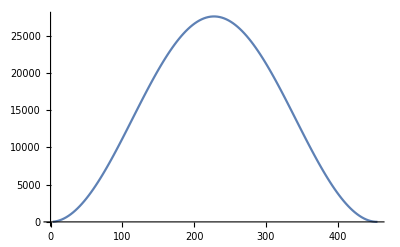

-Graphics-

-Graphics-

-Graphics-

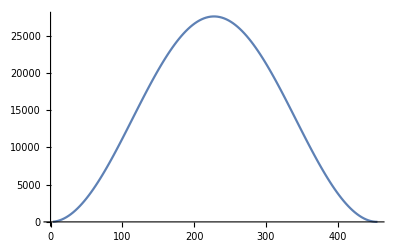

-Graphics-

```mathematica
(* translate to multipole number angle=180/l, or l=180/angle *)

anglesaa=Flatten[Table[{180/N[degRad delta/(i delta)]},{i,1,Lbin}]];
anglesbb=Flatten[Table[{180/N[degRad delta/(i delta)]},{i,1,Lbin}]];
angles=Flatten[Table[{180/N[degRad 2 ArcTan[1/2/(i corr)]]},{i,1,Lbin}]];

weightsbb=Flatten[Table[{2 π R^3(1-Cos[i delta]^2+Sin[i delta]^2)delta  rho},{i,1,Lbin}]];
weights=Flatten[Table[{2 π R^3(1-Cos[i delta]^2+Sin[i delta]^2)delta  rho},{i,1,Lbin}]];

entriesaa=Transpose@{anglesaa,weights};ListPlot[entriesaa,Axes->True,Joined->True,PlotRange->All]
ListPlot[entriesaa,Axes->True,Joined->True,PlotRange->{x,0,10}]
entriesbb=Transpose@{anglesbb,weightsbb};ListPlot[entriesbb,Axes->True,Joined->True,PlotRange->All]
ListPlot[entriesbb,Axes->True,Joined->True,PlotRange->{x,0,10}]
entries=Transpose@{angles,weights};
ListPlot[entries,Axes->True,Joined->True,PlotRange->All]
ListPlot[entries,Axes->True,Joined->True,PlotRange->{x,0,10}]
```